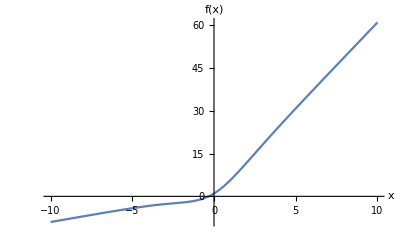

```mathematica
(* setup *)
ftrue[x_]:=1+x(1+5(1+E^(-x))^(-1)); (* modello "vero" dal quale si generano i dati *)
atrue=1; (* In realtà qualunque a > 0 si comporta nello stesso modo; questo è un po' il "problema" di questa funzione obiettivo, ma anche la feature che crea dei minimi con una grande differenza di curvature lungo b; ovviamente è stata scelta in maniera artificiale perché avesse sia minimi molto piccati che minimi molto piatti *)
btrue=5;
fmod[x_,a_,b_]:=x(1+b(1+E^(-a x))^(-1))+a^2; (* NOTA: puoi provare ad aggiungere questo termine a^2 come "penalità" per eliminare gli infiniti minimi con a>0 *)
losssingle[x_,y_,a_,b_]:=(y -fmod[x,a,b])^2; (* questa è solo la parte quadratica, senza somma o normalizzazione*)
gradloss[x_,y_,a_,b_]:={D[(y -fmod[x,a,b])^2,a],D[(y -fmod[x,a,b])^2,b]} ;
Plot[ftrue[x],{x,-10,10},AxesLabel->{"x","f(x)"}]
```

```mathematica
(*generate a sample from ftrue*)nn=30;
ll=20;
ntot=nn ll;(*number of datapoints*)xs=Table[xi-Floor[nn/2],{xi,1,nn}];
fi=Table[N[ftrue[x/.(x->xs[[i]])]],{i,1,Length[xs]}];
eps=3;
epss=RandomReal[{-eps,eps},ll*Length[fi]];
data=Table[{xs[[i]],Table[fi[[i]]+epss[[i+j]],{j,0,ll-1}]},{i,1,Length[fi]}];
```

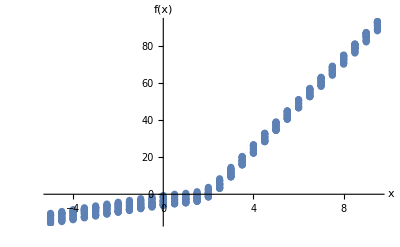

```mathematica
plots = Table[
ListPlot[Table[{0.5i-5.5,data[[i,2]][[j]]},{i,1,nn}],AxesLabel->{"x","f(x)"},PlotRange->All],{j,1,ll}];
Show[plots]
```

```mathematica
(******genero dati per l'errore di generalizzazione************)
nnp=Floor[N[nn/5]];
llp=Floor[N[ll/5]];
ntotp=nnp llp;(*number of datapoints*)xsp=Table[xi-Floor[nnp/2],{xi,1,nnp}];
fip=Table[N[ftrue[x/.(x->xsp[[i]])]],{i,1,Length[xsp]}];
epssp=RandomReal[{-eps,eps},llp*Length[fip]];
datap=Table[{xsp[[i]],Table[fip[[i]]+epssp[[i+j]],{j,0,llp-1}]},{i,1,Length[fip]}];
lossp[a_,b_]:=(1/ntotp)*Sum[Sum[(datap[[i,2]][[j]]-fmod[datap[[i,1]],a,b])^2,{j,1,llp}],{i,1,nnp}];(*loss function per il validation set*)(************************************************************)loss[a_,b_]:=(1/ntot)*Sum[Sum[(data[[i,2]][[j]]-fmod[data[[i,1]],a,b])^2,{j,1,ll}],{i,1,nn}];
areal=x/.Last[FindMinimum[{loss[x,y],Abs[x]≤1.5atrue&&Abs[y]≤1btrue},{x,y}]];
breal=y/.Last[FindMinimum[{loss[x,y],Abs[x]≤1.5 atrue&&Abs[y]≤1btrue},{x,y}]];

(*Trovo il minimo negativo della funzione*)
arealmin=x/.Last[FindMinimum[{loss[x,y],x<0},{x,y}]];
brealmin=y/.Last[FindMinimum[{loss[x,y],x<0},{x,y}]];

(*cerco i punti in cui il gradiente si annulla*)
gradlosstot[a_,b_]:=(1/ntot)*Sum[Sum[gradloss[data[[i,1]],data[[i,2]][[j]],x,y],{j,1,ll}],{i,1,nn}]/.{x->a,y->b};
asaddleprecise=x/.FindRoot[{gradlosstot[x,y][[1]],gradlosstot[x,y][[2]]},{{x,-0.6},{y,25/6}}];
bsaddleprecise=y/.FindRoot[{gradlosstot[x,y][[1]],gradlosstot[x,y][[2]]},{{x,-0.6},{y,25/6}}];

hessloss[x_,y_,a_,b_]:={{D[D[(y-fmod[x,a,b])^2,a],a],D[D[(y-fmod[x,a,b])^2,a],b]},{D[D[(y-fmod[x,a,b])^2,b],a],D[D[(y-fmod[x,a,b])^2,b],b]}};

hesslosssaddle=Sum[Sum[hessloss[data[[i,1]],data[[i,2]][[j]],x,y]/.{x->asaddleprecise,y->bsaddleprecise},{j,1,ll}],{i,1,nn}];
Print[Eigenvalues[hesslosssaddle]];
{-224818.,66667.5}
```

{-220204.,65212.1}

{-224818.,66667.5}

```mathematica
eta=0.00001;
bsize=1;
U[a_,b_]:= Log[loss[x,y]]/.{x->a,y->b};
T= 100;
Pstat[a_,b_]:=Exp[-U[x,y]/T]*(loss[x,y])^(-1)/.{x->a,y->b}; 
q=6;
(*Plot3D[Pstat[a,b],{a,-8,4},{b,0,7}, AxesLabel->{"a","b"},PlotRange->All]*)
```

```mathematica
Plot3D[Pstat[a,b],{a,-8,-2},{b,0-1,7}, AxesLabel->{"a","b","P_s(a,b)"},PlotRange->All]
```

-Graphics3D-

General::munfl: 1/((2.89064×10^6)^100001.) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

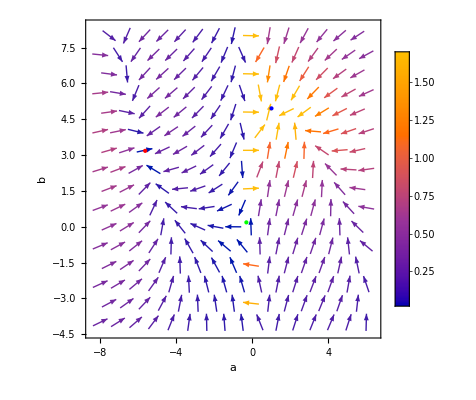

General::munfl: 1/((1.50815×10^6)^100001.) is too small to represent as a normalized machine number; precision may be lost.

$Aborted

```mathematica
eta=0.00001;
bsize=1;
hesslossmin= Sum[Sum[hessloss[data[[i,1]],data[[i,2]][[j]],x,y]/.{x->areal,y->breal},{j,1,ll}],{i,1,nn}];

partialx[a_,b_]:=-D[loss[x,y],x]*Pstat[x,y]-(eta)/(bsize)*(hesslossmin[[1]][[1]]*D[loss[x,y]*Pstat[x,y],x]+hesslossmin[[1]][[2]]*D[loss[x,y]*Pstat[x,y],y])/.{x->a,y->b};
partialy[a_,b_]:=-D[loss[x,y],y]*Pstat[x,y]-(eta/bsize)*(hesslossmin[[2]][[1]]*D[loss[x,y]*Pstat[x,y],x]+hesslossmin[[2]][[2]]*D[loss[x,y]*Pstat[x,y],y])/.{x->a,y->b};


J[a_,b_]:={partialx[x,y],partialy[x,y]} /.{x->a,y->b};
r=8;
vplot=VectorPlot[J[a,b],{a,-r,6}, {b,-4,r},FrameLabel->{"a","b"},PlotLegends->Automatic];
g=Graphics[{PointSize[Large],Blue,Point[{areal,breal}]}];
locmin=Graphics[{PointSize[Large],Red,Point[{arealmin,brealmin}]}];
locsad=Graphics[{PointSize[Large],Green,Point[{asaddleprecise,bsaddleprecise}]}];
Show[vplot,g, locmin,locsad]
```

```mathematica
numeta=Table[i,{i,4,4}];
numpath=20;
bsize =1;
etasgd=0.00001;
(*simulo le traiettorie con la SDE con vari punti iniziali e guardo la distribuzione delle posizioni *)
timestep=etasgd;
maxtimes=1000;
bsizesgd =bsize;
(*vc= Table[{0,0},{i,1,numpath*maxtimes}];*)



(*calcolo l'hessiano, lo valuto su tutto il set e nel punto di minimo nello spazio dei parametri(che conosco)*)
hessloss[x_,y_,a_,b_]:= {{D[D[(y -fmod[x,a,b])^2,a],a],D[D[(y -fmod[x,a,b])^2,a],b]},{D[D[(y -fmod[x,a,b])^2,b],a],D[D[(y -fmod[x,a,b])^2,b],b]}};


(*vauluto l'hessiano nel minimo reale*)
hesslossmin= Sum[Sum[hessloss[data[[i,1]],data[[i,2]][[j]],x,y]/.{x->areal,y->breal},{j,1,ll}],{i,1,nn}];
sqrthesslossmin=MatrixPower[ hesslossmin, 1/2];

(*calcolo il gradiente su tutto il set di dati*)
gradlosstot[a_,b_]:=(1/ntot)*Sum[Sum[gradloss[data[[i,1]],data[[i,2]][[j]],x,y],{j,1,ll}],{i,1,nn}]/.{x->a,y->b}
w=8;
(*calcolo la dinamica*)
vc={RandomReal[{-6,6}],RandomReal[{-1,6}]};
vprev=vc;
vcurrent=vprev;
```

```mathematica
startingp=Table[{RandomReal[{-6,6}],RandomReal[{-1,6}]},{i,1,numpath}]
```

{{-1.90159,-0.923051},{2.68598,2.69447},{-5.98906,2.3675},{5.80276,1.2996},{-5.72807,-0.789449},{0.805546,3.84206},{-0.118786,4.28206},{5.78704,0.0845382},{-3.44181,1.11785},{-3.44222,4.50553},{-1.97655,5.40395},{1.23798,-0.634834},{-2.1506,-0.828004},{1.18193,-0.504612},{-5.20092,1.70545},{-2.6418,-0.737842},{2.80882,3.83659},{2.13324,4.56165},{0.036667,2.97164},{-1.07504,2.46009}}

```mathematica
countpath=1
For[ite=2,ite≤numpath*maxtimes, ite++,
If[Mod[ite,maxtimes]==0,vcurrent={RandomReal[{-6,6}],RandomReal[{-1,6}]}, 
vprev=vcurrent;
Z={RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]};
Zscale= sqrthesslossmin.Z;
ai= vprev[[1]];
bi= vprev[[2]];
vcurrent[[1]]= ai-gradlosstot[x,y][[1]]*timestep+Sqrt[(2*etasgd/bsizesgd)*loss[x,y]]*Zscale[[1]]*Sqrt[timestep]/.{x->ai,y->bi};
vcurrent[[2]]= bi-gradlosstot[x,y][[2]]*timestep+Sqrt[(2*etasgd/bsizesgd)*loss[x,y]]*Zscale[[2]]*Sqrt[timestep]/.{x->ai,y->bi};
If[Mod[ite,100]==0, Print[ite, ", ", vcurrent]];
If[Mod[ite,10]==0, vc=Append[vc,vcurrent]];
];
]
```

1

100, {-5.83218,0.35935}

200, {-5.7654,0.465531}

300, {-5.53218,-1.66598}

400, {-5.45683,-0.75139}

500, {-5.24808,-0.212148}

600, {-5.18195,0.879228}

700, {-4.75552,0.629932}

800, {-5.42758,-0.450003}

900, {-4.90446,0.203558}

1100, {5.17062,-0.597574}

1200, {5.1662,0.450051}

1300, {4.8714,0.897452}

1400, {5.14979,1.93745}

1500, {4.48028,1.2483}

1600, {4.49492,1.87525}

1700, {4.04167,2.43306}

1800, {4.0459,3.25909}

1900, {3.98199,3.66145}

2100, {0.274092,2.08404}

2200, {0.383039,1.63586}

2300, {0.595997,2.67649}

2400, {0.803535,3.42377}

2500, {0.601852,2.55208}

2600, {0.763615,3.34335}

2700, {0.640107,2.93997}

2800, {0.761431,3.26306}

2900, {0.888749,3.53002}

3100, {4.15842,2.58839}

3200, {4.46,3.46219}

3300, {4.26864,3.85749}

3400, {4.16728,3.76064}

3500, {3.96446,3.9731}

3600, {3.70811,3.89016}

3700, {3.65628,3.68522}

3800, {3.37271,3.27372}

3900, {3.19586,2.90348}

4100, {4.62103,5.70962}

4200, {4.22967,4.79555}

4300, {3.91187,4.51048}

4400, {3.84877,4.70844}

4500, {3.6249,5.19609}

4600, {3.41082,5.38993}

4700, {3.26499,5.37106}

4800, {3.11115,5.58674}

4900, {2.95622,5.41671}

5100, {-5.8516,-0.697649}

5200, {-4.98136,0.90798}

5300, {-5.3515,0.382814}

5400, {-5.28613,-0.559941}

5500, {-5.41552,-1.1565}

5600, {-4.83868,0.891969}

5700, {-4.94863,1.18232}

5800, {-4.64883,2.3038}

5900, {-4.76199,2.40778}

6100, {-1.97482,3.51087}

6200, {-1.86863,3.01464}

6300, {-1.7767,4.09228}

6400, {-2.29518,4.57447}

6500, {-2.78369,4.61215}

6600, {-2.88744,5.07605}

6700, {-3.60133,4.20416}

6800, {-4.0883,4.40989}

6900, {-4.89784,4.7236}

7100, {-3.79859,3.51387}

7200, {-3.84766,4.29415}

7300, {-4.30224,4.35973}

7400, {-4.90352,3.58215}

7500, {-5.37884,2.9448}

7600, {-5.23699,2.96599}

7700, {-5.64036,3.70889}

7800, {-5.32606,3.59207}

7900, {-4.97861,4.41567}

8100, {4.59634,0.0491743}

8200, {4.76708,1.05731}

8300, {4.7088,0.409115}

8400, {4.68534,0.539976}

8500, {4.61016,1.0449}

8600, {4.24431,0.954594}

8700, {4.40268,0.492641}

8800, {4.2806,1.58282}

8900, {4.28926,1.8574}

9100, {0.994417,4.93537}

9200, {0.960766,4.93447}

9300, {0.961011,4.86213}

9400, {0.98323,4.93829}

9500, {0.978694,4.98934}

9600, {0.985365,5.04613}

9700, {0.987281,4.98642}

9800, {1.00795,5.03741}

9900, {1.01776,5.08025}

10100, {4.26676,2.74614}

10200, {4.29757,2.72545}

10300, {3.97732,2.78459}

10400, {4.31356,2.68484}

10500, {4.22322,2.85748}

10600, {4.19548,3.36251}

10700, {3.98134,3.01461}

10800, {3.69493,2.80065}

10900, {3.62891,3.16877}

11100, {-0.615433,2.54031}

11200, {0.150771,3.1756}

11300, {0.552948,3.09196}

11400, {0.490565,2.73916}

11500, {0.561504,3.25119}

11600, {0.479876,3.42791}

11700, {0.626333,3.36385}

11800, {0.6544,3.45341}

11900, {0.890978,3.79284}

12100, {4.21261,4.696}

12200, {4.08943,4.5209}

12300, {3.83205,3.89787}

12400, {3.47564,3.59775}

12500, {3.33312,3.3009}

12600, {3.21429,2.90333}

12700, {3.16807,2.77342}

12800, {3.28662,2.91962}

12900, {3.24188,3.0313}

13100, {4.12652,-1.27022}

13200, {4.4403,0.209519}

13300, {4.44712,-0.661282}

13400, {4.28404,-1.21772}

13500, {4.41543,0.119209}

13600, {3.88309,-0.814105}

13700, {3.63661,0.350007}

13800, {3.66908,1.73617}

13900, {3.90279,2.08767}

14100, {5.20061,0.778481}

14200, {5.00736,0.476337}

14300, {4.86943,1.22471}

14400, {4.95238,1.47963}

14500, {4.76123,1.13664}

14600, {5.03858,1.4155}

14700, {5.097,3.00927}

14800, {5.17091,2.83066}

14900, {5.28032,3.52885}

15100, {2.20042,5.47622}

15200, {2.30159,5.5132}

15300, {2.1199,5.29828}

15400, {2.09996,5.06632}

15500, {2.00802,4.98711}

15600, {2.05698,4.96348}

15700, {1.97205,4.83419}

15800, {1.9357,4.76182}

15900, {1.8887,4.76093}

16100, {-5.27033,3.84499}

16200, {-5.27266,3.88575}

16300, {-5.52312,3.45268}

16400, {-5.24288,4.24777}

16500, {-5.56435,3.78679}

16600, {-5.60868,4.53858}

16700, {-5.6558,4.76077}

16800, {-5.40221,5.81253}

16900, {-5.59795,6.32769}

17100, {3.40981,1.77043}

17200, {3.03653,1.55664}

17300, {2.95008,1.58048}

17400, {2.97039,1.6025}

17500, {2.97436,1.35458}

17600, {3.05483,1.4137}

17700, {3.0749,1.18543}

17800, {2.88894,1.27568}

17900, {3.34655,1.96059}

18100, {-6.32783,3.78133}

18200, {-6.30826,3.27897}

18300, {-6.50958,2.52287}

18400, {-6.02806,2.33098}

18500, {-5.63104,3.10154}

18600, {-5.64218,3.46342}

18700, {-5.6204,3.5323}

18800, {-5.94564,3.51325}

18900, {-5.81933,4.40095}

19100, {5.24745,2.17098}

19200, {4.82718,2.83822}

19300, {4.76685,2.63266}

19400, {4.54192,2.65594}

19500, {4.38804,2.4295}

19600, {4.14948,2.16561}

19700, {3.64757,1.33011}

19800, {3.66687,0.421637}

19900, {3.92882,1.05532}

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop","histsimpstaz.mx"}],vc]
```

C:\Users\jackv\Desktop\histsimpstaz.mx

Part::partd: Part specification 4.80752⟦1⟧ is longer than depth of object.

Part::partd: Part specification 4.80752⟦2⟧ is longer than depth of object.

Part::partd: Part specification 3.30108⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

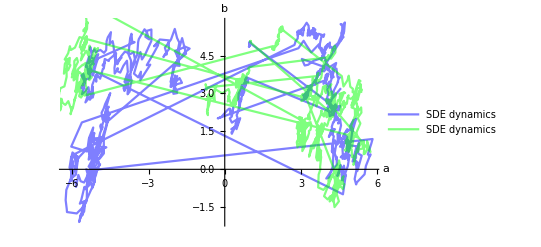

```mathematica
(*grafico sul piano le traiettorie*)
plt1=ListLinePlot[Table[{vc[[ite]][[1]],vc[[ite]][[2]]},{ite,1,maxtimes-1}],PlotLegends->{"SDE dynamics"},PlotStyle->{Blue,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All];
plt2=ListLinePlot[Table[{vc[[ite]][[1]],vc[[ite]][[2]]},{ite,maxtimes,2*maxtimes-1}],PlotLegends->{"SDE dynamics"},PlotStyle->{Green,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All];
Show[plt1,plt2]
```

```mathematica
vc
```

{{-7.41937,5.78094},{-7.46395,5.82193},{-7.51023,5.73187},{-7.54127,5.79325},{-7.51112,5.91866},{-7.50933,5.89531},{-7.46697,5.95141},{-7.46114,6.01166},39984,{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}
 |  |  |  |

```mathematica
(*Istogramma 3d dei dati*)
Histogram3D[vc, AxesLabel->{"a","b"}]
```

-Graphics3D-

```mathematica
s=20;
xgrid=Subdivide[0.5,1.5,s];
ygrid= Subdivide[4.5,5.5,s];
grid = Outer[List,xgrid,ygrid];
vectorgrid= ArrayReshape[grid, {(s+1)^2,2}];
sampling=Table[Pstat[vectorgrid[[i]][[1]],Pstat[[i]][[2]]],{i,1,(s+1)^2}];
samplingscatter=Table[{vectorgrid[[i]][[1]],vectorgrid[[i]][[2]],sampling[[i]]},{i,1,(s+1)^2}];
(*ListDensityPlot[samplingscatter,AxesLabel->{"a","b"}]*)
```

```mathematica
PearsonChiSquareTest[vc[[1;;23000]],Pstat[]]
```

PearsonChiSquareTest::rctnlndst: The argument Pstat[] at position 2 should be a valid distribution or a rectangular array of real numbers with length greater than the dimension of the array. The dimensionality of the arguments at positions 1 and 2 must match.

PearsonChiSquareTest[{{1.73746,7.37024},{1.70491,7.37214},{1.70894,7.43351},{1.70792,7.36881},22993,{0.585891,5.13416},{0.586901,5.13465},{-1.92206,5.523}},Pstat[]]
 |  |  |  |